```mathematica
(*
1. Data backup.
2. Preserve this code: valid for Tanay-Stein-Ghersi 1.5PN paper with σ1=(1+(3/4) (m2/m1))  σ2=(1+(3/4)  (m1/m2)).
3. Racine, Gerosa: Re-interpretation of Seff.L = (σ1 S1 + σ2 S2).L
where
σ1=(1+ m2/m1)  σ2=(1+  m1/m2).

Check with Tom's code.

4. Run the code again. Find new minima.
5. Hopefully, the minima are not at the boundaries of the phase space, i.e. they are crossable. Think of vector rotation schemes which lets us cross the separatrix. Already done before. 
6. Your plan to cross separatrix by keeping Seff.L fixed and changing J by only changing Δϕ does not work if Δϕ is on the boundary (0 or 2 π). So, find a better optimal point for this to work.
7. Or change Seff.L while keeping J constant: rotate S1, S2 about S = S1+S2.

8. If these don't work: Hunt for minima using ContourPlot3D(3 angle space) or ContourPlot(2 (J, Seff.L) space); example below. Advantage: you simply need to cross this boundary without keeping J or SeffdL constants (i.e. moving horizontally/vertically only). Hence more freedom in perturbing the optimal configuration.

9. Evolve system on these 2 points straddling the separatrix: hopefully they diverge at some point.
*)
```

```mathematica
(*ContourPlot[x^2+ y^2==1,{x,-1.5,1.5}, {y,0,1}]
ContourPlot3D[x^2+ y^2 +z^2==1,{x,-1.5,1.5}, {y,0,1}, {z,0,1}]*)
```

```mathematica
L=7/10  ;
S1=3/10  ;
S2=4/10 ;
(*0<=J<=√(2L S1+2L S2+S1 S2)*)
```

If m_1,m_2>0 and m_1>m_2, then 0<σ_1<1.75

```mathematica
σ1=15/10   ; (*σ1=1.5*)
0<σ<175/100/.σ->σ1
```

True

### Parameter definitions

```mathematica
Δ1 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ2)/(σ1-σ2);
Δ2 = ((J^2-L^2-S1^2-S2^2)/2  -   SeffdL/σ1)/(σ1-σ2);
σ2 = 1+((*9*)1)/((*16*) (-1+σ1))   ;

(*σ1=(1+ m2/m1)  σ2=(1+  m1/m2)*)
(* Not this σ1=(1+3/4 m2/m1)  σ2=(1+3/4  m1/m2)*)
```

### Cubic function roots

```mathematica
cubic =    Expand[ L^2 S1^2 S2^2- 2 σ1 σ2 (σ1-σ2)f(f-Δ1)(f-Δ2)-L^2(σ1-σ2)^2 f^2-S2^2 σ2^2(f-Δ1)^2-S1^2 σ1^2(f-Δ2)^2  ] (*The cubic polynomial of Eq. 3.1 of Cho-Lee*);
a3=Coefficient[cubic,f^3];
a2=Coefficient[cubic,f^2];
a1=Coefficient[cubic,f];
a0=Expand[cubic-(a3 f^3+a2 f^2+a1 f)];
p=(3 a1 a3-a2^2)/(3 a3^2);
q=(2 a2^3-9a1 a2 a3+27a0 a3^2)/(27 a3^3);
roots=Table[Subscript[f, k]->-a2/(3a3)+2 √(-p/3)Cos[1/3 ArcCos[(3q)/(2p)√(-3/p)]+(2π k)/3],{k,1,3}];
f1=roots[[1,2]];
f2=roots[[2,2]];
f3=roots[[3,2]];
```

### Flow amounts definitions

```mathematica
(*The following definitions are in Cho-Lee*)
```

#### Δλ_(S_eff.L)

```mathematica
A=  2 σ1 σ2 (σ2-σ1) ;
β=√((f2-f1)/(f3-f1)) (*elliptic modulus "k"*);
Δλ1= 4/(√(A(f3-f1)))EllipticK[β];
```

#### Δλ_(J^2)

```mathematica
B1 = 1/2((SeffdL + L^2(σ1+σ2))(J+L)+ L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
B2 = 1/2((SeffdL + L^2(σ1+σ2))(J-L)- L(σ1 S1^2+σ2 S2^2+(σ1+σ2)(Δ2 σ1-Δ1 σ2))) ;
D1=L(L+J)+Δ2 σ1-Δ1 σ2;
D2=L(L-J)+Δ2 σ1-Δ1 σ2;
α1 = ((σ1-σ2)(f2-f1))/(D1-f1(σ1-σ2))  ;
α2 = ((σ1-σ2)(f2-f1))/(D2-f1(σ1-σ2))  ;
Δλ2=-1/(2 J) (4/(√(A(f3-f1)))) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))+(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)));
```

#### Δλ_(L^2)

```mathematica
Δλ3=-1/(2 L)((4/(√(A(f3-f1)))) ((B1  EllipticPi[α1,β^2])/(D1-f1(σ1-σ2))-(B2 EllipticPi[α2,β^2])/(D2-f1(σ1-σ2)))  - (SeffdL +(Δ1-Δ2)σ1 σ2 + L^2(σ1+σ2))Δλ1/L )  ;
```

#### Δλ_(S_1^2)

```mathematica
B1S1= 1/2(-L^2 S1 σ1+J S1^2 σ1-S1^3 σ1-S1 Δ2 σ1^2+J^2 S1 σ2-2 J S1^2 σ2+S1^3 σ2-J Δ1 σ1 σ2+2 S1 Δ1 σ1 σ2+J Δ1 σ2^2-S1 Δ1 σ2^2)  ;
B2S1= 1/2(L^2 S1 σ1+J S1^2 σ1+S1^3 σ1+S1 Δ2 σ1^2-J^2 S1 σ2-2 J S1^2 σ2-S1^3 σ2-J Δ1 σ1 σ2-2 S1 Δ1 σ1 σ2+J Δ1 σ2^2+S1 Δ1 σ2^2)   ;
D1S1=-J S1+S1^2-Δ1 σ2;
D2S1=(J S1+S1^2-Δ1 σ2);

α1S1 = ((-σ1)(f2-f1))/(D1S1+f1 σ1)  ;
α2S1= ((-σ1)(f2-f1))/(D2S1+f1 σ1)  ;
Δλ4=-1/(2 S1)((4/(√(A(f3-f1))))(-(B1S1 EllipticPi[α1S1,β^2])/(D1S1+f1 σ1)+(B2S1 EllipticPi[α2S1,β^2])/(D2S1+f1 σ1))  +  S1(σ2-σ1)Δλ1  )  ;
```

#### Δλ_(S_2^2)

```mathematica
B1S2=1/2(S2 σ2(L^2-J S2+S2^2-Δ1 σ2)-(J-S2)^2 S2 σ1-(J-2S2)Δ2 σ1 σ2+(J-S2)Δ2 σ1^2);
B2S2=1/2(S2 σ2(-L^2-J S2-S2^2+Δ1 σ2)+(J+S2)^2 S2 σ1-(J+2S2)Δ2 σ1 σ2+(J+S2)Δ2 σ1^2);
D1S2=(J-S2)S2-Δ2 σ1;
D2S2=-(J+S2)S2-Δ2 σ1;
α1S2 = ((-σ2)(f2-f1))/(D1S2+f1 σ2)  ;
α2S2= ((-σ2)(f2-f1))/(D2S2+f1 σ2)  ;
Δλ5=-1/(2 S2)((4/(√(A(f3-f1))))(-(B1S2 EllipticPi[α1S2,β^2])/(D1S2+f1 σ2)+(B2S2 EllipticPi[α2S2,β^2])/(D2S2+f1 σ2))  +  S2(σ1-σ2)Δλ1  )  ;
```

### Fifth action J_5

```mathematica
I5=1/π(SeffdL Δλ1+J^2 Δλ2+L^2 Δλ3+S1^2 Δλ4+S2^2 Δλ5);
```

```mathematica
dI5=D[I5,SeffdL];
```

```mathematica
(*(*(*(*(*MinConst=NMinimize[{Abs[1/dI5],J>0,SeffdL>0},{SeffdL,J}]*)*)*)*)*)
```

### Spherical J_5

Assumming  along the  axis, thus

```mathematica
(*SeffdL=σ1 S1dL+σ2 S2dL*)
```

```mathematica
S1dL=S1 L(Cos[θ1] Cos[0]+Sin[θ1] Sin[0] Cos[ϕ1-0])
S2dL=S2 L(Cos[θ2] Cos[0]+Sin[θ2] Sin[0] Cos[ϕ2-0])
S1dS2=S1 S2(Cos[θ1] Cos[θ2]+Sin[θ1] Sin[θ2] Cos[Δϕ])
```

(21 Cos[θ1])/100

(7 Cos[θ2])/25

3/25 (Cos[θ1] Cos[θ2]+Cos[Δϕ] Sin[θ1] Sin[θ2])

```mathematica
dI5sph=dI5/.{SeffdL->(σ1 S1dL+σ2 S2dL)}/.{J->√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))};
```

```mathematica
MinAngles=NMinimize[{Abs[1/dI5sph],1<=θ1<= π, 0<=θ2<=   π, 1/100<=Δϕ<=  49/100   2 π   (*,(σ1 S1dL+σ2 S2dL)>0*)     },{θ1,θ2,Δϕ}, WorkingPrecision->50, PrecisionGoal->30, MaxIterations->500]
```

Power::infy: Infinite expression 1/(0``-2.6277320816521867) encountered.

NMinimize::nnum: The function value ComplexInfinity is not a number at {Δϕ,θ1,θ2} = {1.3840894758986420432601397072982411531213462531716,2.1768038816709391492294685907657097722015014732988,1.994789770458290836449516254681338021814871806124}.

{0.072844280965561776226661894195757440684246830642223,{θ1→2.1768038816711456229717749451682834695756828863855,θ2→1.9947897704582205055356138558726141797580798005328,Δϕ→1.3840894758984623400823998182167020822490680664177}}

```mathematica
Jphys=√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))//.MinAngles[[2]]
```

0.6000000000000001715429879398630545977920929087853

```mathematica
SeffdLphys=(σ1 S1dL+σ2 S2dL)//.MinAngles[[2]]
```

-0.5250000000000000103059432463360204225137376301962

```mathematica
plot3D =Plot3D[Abs[1/dI5] , {J,0.97Jphys, 1.03 Jphys} , {SeffdL , 0.9 SeffdLphys, 1.1 SeffdLphys}]
```

-Graphics3D-

```mathematica
MinAnglesPert = MinAngles[[2]] ;
JphysPert=√(L^2+S1^2+S2^2+2(S1dL+S2dL+S1dS2))//.MinAnglesPert 
SeffdLphysPert=(σ1 S1dL+σ2 S2dL)     //.MinAnglesPert 

verticalLine=Graphics3D[{Red,Thickness[0.01],Line[{{JphysPert,SeffdLphysPert,-6},{JphysPert,SeffdLphysPert,6}}] }];
Show[plot3D,verticalLine]
```

0.6000000000000001715429879398630545977920929087853

-0.5250000000000000103059432463360204225137376301962

-Graphics3D-

```mathematica
Quit[];
```

```mathematica
1000  //Pause
```

```mathematica
Re[1/dI5/.J->Jphys]/.SeffdL->SeffdLphys
Im[1/dI5/.J->Jphys]/.SeffdL->SeffdLphys
```

1.3482×10^-6

0

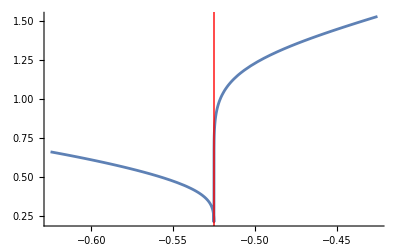

-Graphics-

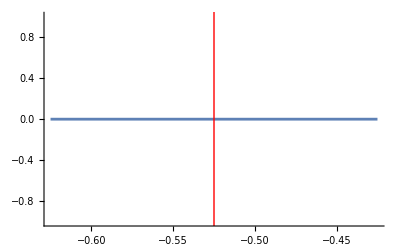

```mathematica
lowLim = SeffdLphys - 0.1; upLim = SeffdLphys + 0.1;
Plot[Abs[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
Plot[Re[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
Plot[Im[1/dI5]/. J->Jphys,{SeffdL,lowLim,upLim},Epilog->{Red,Line[{{SeffdLphys,-10^6},{SeffdLphys,10^6}}]}]
```

```mathematica
lowLim = Jphys - 0.1; upLim = Jphys + 0.1;
Plot[Abs[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
Plot[Re[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
Plot[Im[1/dI5]/. SeffdL->SeffdLphys,{J,lowLim,upLim},Epilog->{Red,Line[{{Jphys,-10^6},{Jphys,10^6}}]}]
```

$Aborted

$Aborted

$Aborted

```mathematica
Elliptic: parabolic (border, catastrophic point):(* hyperbolic (unphysical)*)
```